```mathematica
plotLyrics[lyrics_]:=Module[{wordList},
wordList = StringSplit[StringDelete[lyrics,","]];
MatrixPlot[Table[If[wordList[[i]]==wordList[[j]],1,0],{i,Length[wordList]},{j,Length[wordList]}]]]
```

```mathematica
Lyrics = "Ay 
Fonsi 
DY 
Oh
Oh no, oh no
Oh yeah
Diridiri, dirididi Daddy 
Go
Sí, sabes que ya llevo un rato mirándote 
Tengo que bailar contigo hoy (DY) 
Vi que tu mirada ya estaba llamándome 
Muéstrame el camino que yo voy (Oh)
Tú, tú eres el imán y yo soy el metal 
Me voy acercando y voy armando el plan 
Solo con pensarlo se acelera el pulso (Oh yeah)
Ya, ya me está gustando más de lo normal 
Todos mis sentidos van pidiendo más 
Esto hay que tomarlo sin ningún apuro
Despacito 
Quiero respirar tu cuello despacito 
Deja que te diga cosas al oído 
Para que te acuerdes si no estás conmigo
Despacito 
Quiero desnudarte a besos despacito 
Firmo en las paredes de tu laberinto 
Y hacer de tu cuerpo todo un manuscrito (sube, sube, sube)
(Sube, sube)
Quiero ver bailar tu pelo 
Quiero ser tu ritmo 
Que le enseñes a mi boca 
Tus lugares favoritos (favoritos, favoritos baby)
Déjame sobrepasar tus zonas de peligro 
Hasta provocar tus gritos 
Y que olvides tu apellido (Diridiri, dirididi Daddy)
Si te pido un beso ven dámelo 
Yo sé que estás pensándolo 
Llevo tiempo intentándolo 
Mami, esto es dando y dándolo 
Sabes que tu corazón conmigo te hace bom, bom 
Sabes que esa beba está buscando de mi bom, bom 
Ven prueba de mi boca para ver cómo te sabe 
Quiero, quiero, quiero ver cuánto amor a ti te cabe 
Yo no tengo prisa, yo me quiero dar el viaje 
Empecemos lento, después salvaje
Pasito a pasito, suave suavecito 
Nos vamos pegando poquito a poquito 
Cuando tú me besas con esa destreza 
Veo que eres malicia con delicadeza
Pasito a pasito, suave suavecito 
Nos vamos pegando, poquito a poquito 
Y es que esa belleza es un rompecabezas 
Pero pa montarlo aquí tengo la pieza
Despacito 
Quiero respirar tu cuello despacito 
Deja que te diga cosas al oído 
Para que te acuerdes si no estás conmigo
Despacito 
Quiero desnudarte a besos despacito 
Firmo en las paredes de tu laberinto 
Y hacer de tu cuerpo todo un manuscrito (sube, sube, sube)
(Sube, sube)
Quiero ver bailar tu pelo 
Quiero ser tu ritmo 
Que le enseñes a mi boca 
Tus lugares favoritos (favoritos, favoritos baby)
Déjame sobrepasar tus zonas de peligro 
Hasta provocar tus gritos 
Y que olvides tu apellido
Despacito 
Vamos a hacerlo en una playa en Puerto Rico 
Hasta que las olas griten \"¡ay, bendito!\" 
Para que mi sello se quede contigo
Pasito a pasito, suave suavecito 
Nos vamos pegando, poquito a poquito 
Que le enseñes a mi boca 
Tus lugares favoritos (favoritos, favoritos baby)
Pasito a pasito, suave suavecito 
Nos vamos pegando, poquito a poquito 
Hasta provocar tus gritos 
Y que olvides tu apellido (DY)
Despacito
";
plotLyrics[Lyrics]
```

-Graphics-

```mathematica
Despacito = Quiet[Import[NotebookDirectory[]<>"/Despacito.mid","SoundNotes"]];
```

```mathematica
plotSong[midiData_]:=Module[{track,Instrument,NoteList,numTracks},
numTracks = Length[midiData];
Table[

track  =midiData[[α]];
Instrument = track[[1,3]];
NoteList =track[[All,1]];
{Instrument,MatrixPlot[Table[If[NoteList[[i]]==NoteList[[j]],1,0],{i,Length[NoteList]},{j,Length[NoteList]}],Frame-> None]},{α,2,numTracks}]]
```

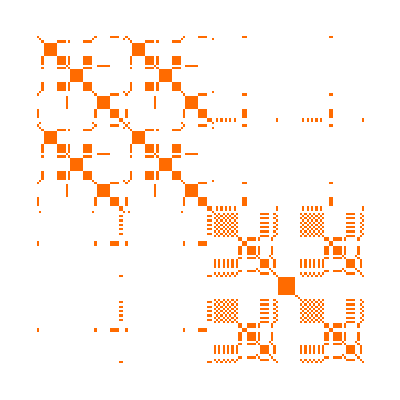
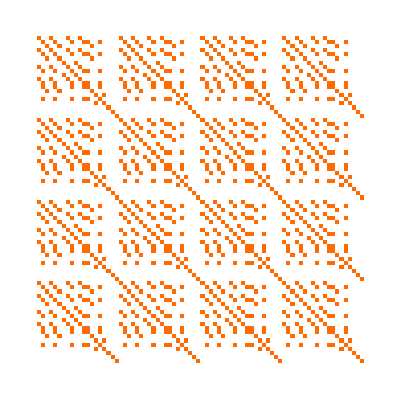
Flute | Bass
-Graphics- | -Graphics-

```mathematica
DespacitoData = plotSong[Despacito];
Grid [Transpose[DespacitoData[[;;-2]]]]
```